```mathematica
GenerationSize=20;
GenerationPairSize=GenerationSize/2;
ChildSize=8;
CreateChild:=Table[RandomInteger[],{i,0,ChildSize-1}];
ChildToNumber[aChild_]:=N[1+Total[Table[2^i,{i,0,ChildSize-1}]*aChild]/2^ChildSize,10];
NumberFitness[aNumber_]:=1-Abs[aNumber^2-2]/2;
GenerationToFitness[aGeneration_]:=Map[NumberFitness[ChildToNumber[#]]&,aGeneration];
ChildPointMutate[aChild_]:=ReplacePart[aChild,RandomInteger[{1,Length[aChild]}]->RandomInteger[]];
ChildrenCrossMutate[aChild_,bChild_]:=
Module[{aPos,bPos,a1,a2,a3,b1,b2,b3,CrossSize},
CrossSize=RandomInteger[{1,Floor[ChildSize/2]}];
aPos=RandomInteger[{1,1+ChildSize-CrossSize}];
bPos=RandomInteger[{1,1+ChildSize-CrossSize}];
a1=aChild[[1;;(aPos-1)]];
a2=aChild[[aPos;;(aPos+CrossSize-1)]];
a3=aChild[[(aPos+CrossSize);;ChildSize]];
b1=bChild[[1;;(bPos-1)]];
b2=bChild[[bPos;;(bPos+CrossSize-1)]];
b3=bChild[[(bPos+CrossSize);;ChildSize]];
{Join[a1,b2,a3],Join[b1,a2,b3]}];
```

```mathematica
CreateChild
ChildToNumber[%]
NumberFitness[%]
N[Sqrt[2],10]
```

{0,1,0,0,1,1,0,0}

1.1953125

0.714385986

1.414213562

```mathematica
Generation1=Table[CreateChild,{GenerationSize}];
Fitness1=GenerationToFitness[Generation1];
bestPosition1=Ordering[Fitness1,-1][[1]];
bestChildEver=Generation1[[bestPosition1]];
bestFitnessEver=Fitness1[[bestPosition1]];
```

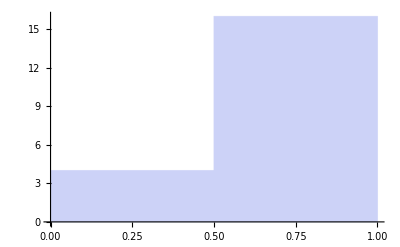

```mathematica
Histogram[Fitness1]
```

```mathematica
generationNumber=1;
previousGeneration=Generation1;
previousFitness=Fitness1;
```

```mathematica
Print["BestEver    = ",ChildToNumber[bestChildEver]];
Print["BestEver^2  = ",ChildToNumber[bestChildEver]^2];
Print["BestFitness = ",bestFitnessEver];
```

BestEver    = 1.40234375

BestEver^2  = 1.96656799

BestFitness = 0.983283997

Real        = 1.414213562

Generation  = 8

BestThis    = 1.37890625

BestThis^2  = 1.90138245

BestFitThis = 0.950691223

BestEver    = 1.4140625

BestEver^2  = 1.99957275

BestFitness = 0.999786377

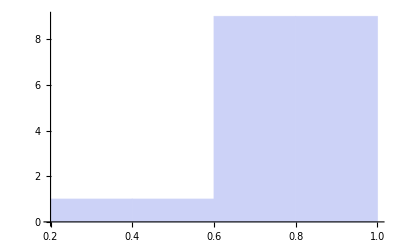

```mathematica
nextGeneration=RandomSample[previousFitness->previousGeneration,Floor[3*GenerationSize/5]];
nextGeneration=Join[nextGeneration,RandomChoice[previousFitness->previousGeneration,GenerationSize-Length[nextGeneration]]];
nextGenerationPairs=
Transpose[
{nextGeneration[[1;;GenerationPairSize]],
nextGeneration[[GenerationPairSize+1;;GenerationSize]]}];
nextGenerationPairs=Map[ChildrenCrossMutate[#[[1]],#[[2]]]&,nextGenerationPairs];
nextGeneration=Join[Transpose[nextGenerationPairs][[1]],Transpose[nextGenerationPairs][[2]]];
nextGeneration=Map[ChildPointMutate,nextGeneration];
nextFitness=GenerationToFitness[nextGeneration];
bestPositionThisGen=Ordering[nextFitness,-1][[1]];
bestChildThisGen=nextGeneration[[bestPositionThisGen]];
bestFitnessThisGen=nextFitness[[bestPositionThisGen]];
If[bestFitnessThisGen>bestFitnessEver,bestChildEver=bestChildThisGen;bestFitnessEver=bestFitnessThisGen;];
generationNumber=generationNumber+1;
previousGeneration=nextGeneration;
previousFitness=nextFitness;
Print["Real        = ",N[Sqrt[2],10]];
Print[];
Print["Generation  = ",generationNumber];
Print["BestThis    = ",ChildToNumber[bestChildThisGen]];
Print["BestThis^2  = ",ChildToNumber[bestChildThisGen]^2];
Print["BestFitThis = ",bestFitnessThisGen];
Print[];
Print["BestEver    = ",ChildToNumber[bestChildEver]];
Print["BestEver^2  = ",ChildToNumber[bestChildEver]^2];
Print["BestFitness = ",bestFitnessEver];
Histogram[nextFitness]
```